## Maximum copula

```mathematica
A=1.1;Plot3D[c[x,y,1,A],{x,0,1},{y,0,1},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
SeedRandom[];
```

```mathematica
Y=.
```

```mathematica
U={};A=10;
Timing[For[i=0,i<10000,i++,
x=RandomReal[];
y=f1[x,RandomReal[],A];
z=f2[x,y,RandomReal[],A];
AppendTo[U,{x,y,z}]]]
ListPointPlot3D[U,AspectRatio->1]
```

{6.9,Null}

-Graphics3D-

```mathematica
U[[4]]
```

{0.170666,0.0953471,0.0502946}

```mathematica
M={};m={};l=Length[U];h=1/15;
For[i=0,i≤1,i+=h,
For[j=0,j≤1,j+=h,
For[k=0,k≤1,k+=h,
AppendTo[m,Length[Select[U,#[[1]]≤i && #[[2]]≤j&& #[[3]]≤k&]]/l-c[i,j,k,A]//N]
]
]];m=Sort[m];
```

```mathematica
m[[3]]
```

0.

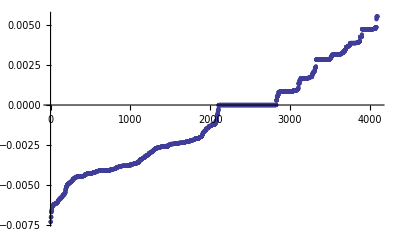

```mathematica
ListPlot[m]
```

```mathematica
ListPlot3D[M]
```

-Graphics3D-

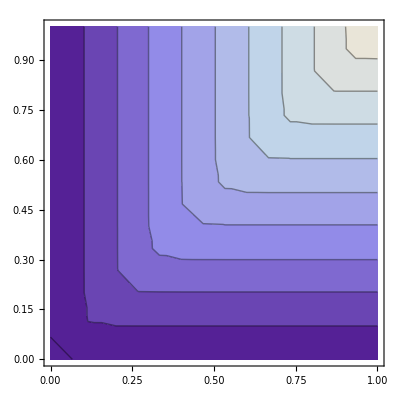

```mathematica
ListContourPlot[M]
```

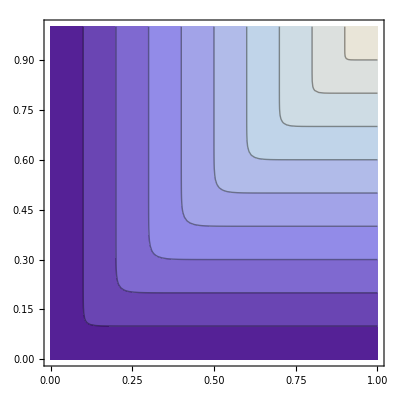

```mathematica
ContourPlot[c[x,y,15],{x,0,1},{y,0,1}]
```

```mathematica
f1=Compile[{{x,_Real},{Z2,_Real},{a,_Real}},ⅇ^(-(-(-Log[x])^a+((-1+a) ProductLog[((-x Z2 (-Log[x])^-a Log[x])^(-1/(-1+a)))/(-1+a)])^a)^(1/a))];
```

```mathematica
Exit[]
```

```mathematica
c[x_,y_,z_,a_]:=Exp[-((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)]
```

```mathematica
Simplify[D[c[x,y,1,a],x]]
```

(ⅇ^(-((-Log[x])^a+(-Log[y])^a)^(1/a)) (-Log[x])^(-1+a) ((-Log[x])^a+(-Log[y])^a)^(-1+1/a))/x

```mathematica
Solve[%==Z2,y]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→ⅇ^(-(-(-Log[x])^a+((-1+a) ProductLog[((-x Z2 (-Log[x])^-a Log[x])^(-1/(-1+a)))/(-1+a)])^a)^(1/a))}}

```mathematica
a=.
```

```mathematica
z=.
```

```mathematica
x=.;y=.
```

```mathematica
Simplify[D[D[c[x,y,z,a],x],y]/D[D[c[x,y,1,a],x],y]]
```

(ⅇ^(((-Log[x])^a+(-Log[y])^a)^(1/a)-((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)) (-1+a+((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)) (((-Log[x])^a+(-Log[y])^a)/((-Log[x])^a+(-Log[y])^a+(-Log[z])^a))^(2-1/a))/(-1+a+((-Log[x])^a+(-Log[y])^a)^(1/a))

```mathematica
Solve[%==Z3,z]
```

```mathematica
f2[x_,y_,Z3_,a_]:=FindRoot[c2[x,y,z,a]==Z3,{z,0.5}][[1,2]]
```

```mathematica
Clear[f2]
```

```mathematica
c2[x_,y_,z_,a_]:=(ⅇ^(((-Log[x])^a+(-Log[y])^a)^(1/a)-((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)) (-1+a+((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)) (((-Log[x])^a+(-Log[y])^a)/((-Log[x])^a+(-Log[y])^a+(-Log[z])^a))^(2-1/a))/(-1+a+((-Log[x])^a+(-Log[y])^a)^(1/a))
```

```mathematica
f2[x_,y_,z3_,a_]:=FindRoot[c2[x,y,z,a]-z3,{z,0.0000000000001,1},Method->"Brent"][[1,2]]
```

```mathematica
Clear[z]
```

```mathematica
Exit[]
```

```mathematica
c2[xx,yy,z,3]
```

1.38392 ⅇ^(1.35983-(2.51453-Log[z]^3)^(1/3)) (1/(2.51453-Log[z]^3))^(5/3) (2+(2.51453-Log[z]^3)^(1/3))

```mathematica
FindRoot[c2[xx,yy,z,3]==0.1,{z,0.5}]
```

{z→0.177796}

```mathematica
f2[.1,0.3,0.1,3]
```

0.0600909

```mathematica
3
```

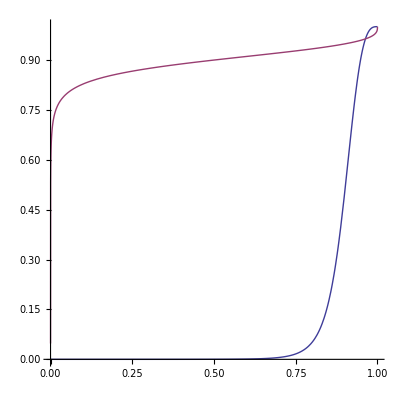

```mathematica
xx=0.9;yy=0.9;Plot[{c2[xx,yy,y,3],f[xx,yy,y,3]},{y,0,1},AspectRatio->1]
```

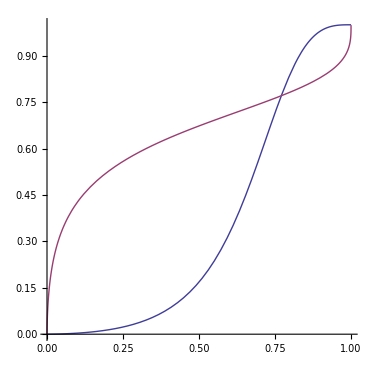

```mathematica
xx=0.7;A=3;Plot[{D[c[x,y,A],x]/.x->xx,f[y,A,xx]},{y,0,1},PlotRange->All,AspectRatio->1]
```

```mathematica
D[c[x,y,A],x]
```

```mathematica
f[AA,BB,CC]
```

ⅇ^(-(-(-Log[CC])^BB+((-1+BB) ProductLog[((-AA CC (-Log[CC])^-BB Log[CC])^(-1/(-1+BB)))/(-1+BB)])^BB)^(1/BB))

```mathematica
Solve[D[c[x,y,A],x]==Z,y]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→ⅇ^(-(-(-Log[x])^A+((-1+A) ProductLog[((-x Z (-Log[x])^-A Log[x])^(-1/(-1+A)))/(-1+A)])^A)^(1/A))}}

```mathematica
$Assumptions=a>1 && 0<Z<1 && 0<x<1&& 0<y<1&& 0<z<1&& 0<Z1<1&& 0<Z2<1&& A>1
```

a>1&&0<Z<1&&0<z<1&&0<Z1<1&&0<Z2<1

```mathematica
a=.
```

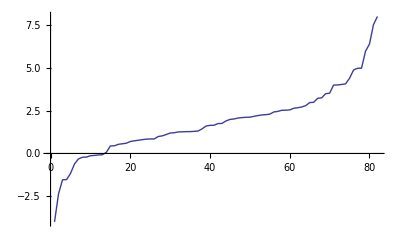

82

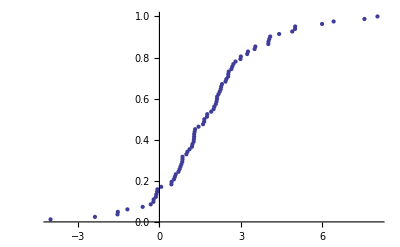

```mathematica
U=Sort[RandomReal[NormalDistribution[2,2],82]];
ListPlot[U,Joined->True]
n=Length[U]
F=Table[{U[[i]],i/n},{i,1,n}];
ListPlot[F]
```

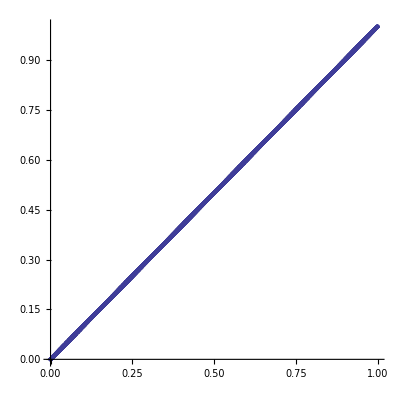

```mathematica
ListPlot[U,AspectRatio->1]
```

```mathematica
F[a_,b_]:=10000-Sort[Tally[UnitStep[a-#1[[2]]]UnitStep[b-#1[[1]]]&/@U],#1[[1]]<#2[[1]]&][[1,2]]
```

```mathematica
Sort[Tally[UnitStep[20/20-#1[[2]]]UnitStep[20/20-#1[[1]]]&/@U],#1[[1]]<#2[[1]]&]
```

{{1,10000}}

```mathematica
n=40;G={};
For[i=0,i<n,i++,
For[j=0,j<n,j++,
AppendTo[G,{i/n,j/n,F[i/n,j/n]}];
]]
```

```mathematica
G[[3]]
```

{0,1/10,0}

```mathematica
ListPlot3D[G,PlotRange->All,BoxRatios->{1,1,1}]
```

-Graphics3D-